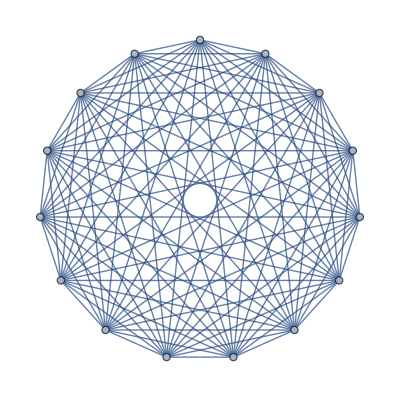

```mathematica
redpequena=RandomGraph[{15,105}]
```

```mathematica
Map[Count,FindCycle[redpequena,3,All]]
```

{Count[{3<->7,7<->8,8<->3}],Count[{3<->8,8<->4,4<->3}],Count[{5<->8,8<->3,3<->5}],Count[{6<->7,7<->8,8<->6}],Count[{6<->4,4<->8,8<->6}],Count[{5<->8,8<->7,7<->5}],Count[{5<->3,3<->7,7<->5}],Count[{2<->7,7<->8,8<->2}],Count[{1<->7,7<->2,2<->1}],Count[{1<->7,7<->5,5<->1}]}

```mathematica
Length[FindCycle[redpequena,{6},All]]
```

300300

```mathematica
linksToAchieveCompleteGraph[nodes_]:=(nodes*(nodes-1))/2;
```

```mathematica
linksToAchieveCompleteGraph[30]
```

435

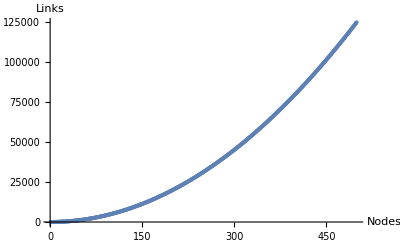

```mathematica
ListPlot[Table[linksToAchieveCompleteGraph[i],{i,2,500,1}],AxesLabel->{"Nodes","Links"}]
```

Probar con redes en las cuales sea posible el calculo de todos sus ciclos para asi comparar con las de tipo aleatoria

```mathematica
SetDirectory[NotebookDirectory[]];
```

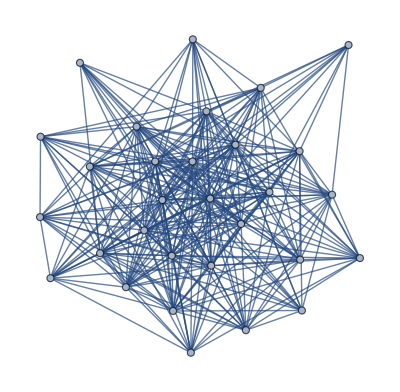

```mathematica
testRed=Import[File["network-30-3-1500.g6"]]
```

```mathematica
EdgeCount[testRed]
```

305

```mathematica
Length[FindCycle[testRed,{3},All]]
```

1599

```mathematica
io=RandomGraph[{VertexCount[testRed],EdgeCount[testRed]}];
```

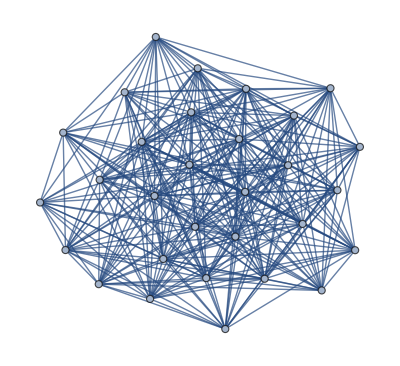

```mathematica
io
```

Cycle length | Number of | Random Network

```mathematica
{{3, 1399}, {4, 19901}, {5, 289546}, {6, 4211609}}
```

Cycle length | Number of | Model Network

```mathematica
{{3, 1599}, {4, 23482}, {5, 351472}, {6, 5231075}}
```

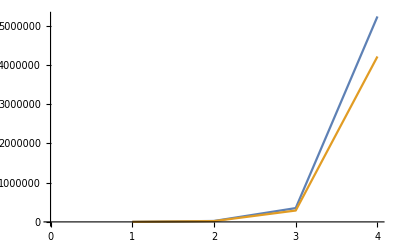

```mathematica
ListLinePlot[{{1599,23482,351472,5231075},{1399,19901,289546,4211609}}]
```

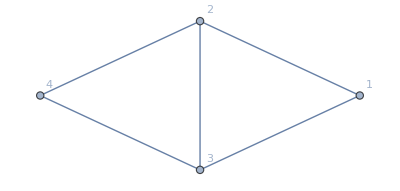

```mathematica
trebol=RandomGraph[{4,5},VertexLabels->"Name"]
```

```mathematica
Length[FindCycle[trebol,{4},All]]
```

1

```mathematica
A=AdjacencyMatrix[trebol];
```

```mathematica
MatrixForm[A]
```

(0 | 1 | 1 | 0
1 | 0 | 1 | 1
1 | 1 | 0 | 1
0 | 1 | 1 | 0)

```mathematica
uio=Dot[A,A,A,A];
```

```mathematica
MatrixForm[uio]
```

(10 | 9 | 9 | 10
9 | 15 | 14 | 9
9 | 14 | 15 | 9
10 | 9 | 9 | 10)

```mathematica
uio[[2]][[2]]
```

15

```mathematica
Sum[uio[[i]][[i]]-5,{i,4}]
```

30

```mathematica
Tr[uio]
```

50

```mathematica
192/32
```

6

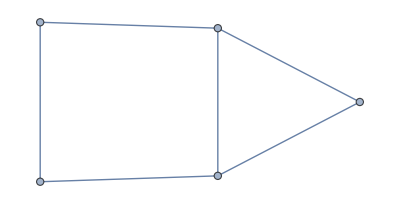

```mathematica
numberofwalksoflength4=Graph[{1<->2,1<->3,2<->3,2<->4,4<->5,3<->5}]
```

```mathematica
adjMat=AdjacencyMatrix[numberofwalksoflength4];
```

```mathematica
Tr[Dot[adjMat,adjMat,adjMat]]
```

6

```mathematica
lamasgrande=Import[File["C:\\Users\\usuario\\Documents\\Trabajo de Grado I\\Modelo\\Redes\\Ciclos\\network-1000-5-10000.g6"]];
```

```mathematica
EdgeCount[lamasgrande]
```

73249

```mathematica
linksToAchieveCompleteGraph[1000]
```

499500

```mathematica
ademil=AdjacencyMatrix[lamasgrande];
```

```mathematica
acom=Dot[ademil,ademil,ademil];
```

```mathematica
Tr[acom]
```

```mathematica
7196352/6
```

1199392

Función que recibe como entrada un grafo y devuelve la cantidad de ciclos de longitud 3 presentes en él

```mathematica
nGC3[g_]:=Module[{adjmatrix,matrix3,amountResult},
adjmatrix=AdjacencyMatrix[g];
matrix3=MatrixPower[adjmatrix,3];
amountResult=Tr[matrix3]/6;
Return[amountResult]
];
```

Función que recibe como entrada un grafo y encuentra la cantidad de ciclos de longitud 4

```mathematica
nGC4[g_]:=Module[{adjmatrix,matrix4, amountResult,sumatoria},
adjmatrix=AdjacencyMatrix[g];
matrix4=MatrixPower[adjmatrix,4];sumatoria=Sum[(VertexDegree[g,i]*(VertexDegree[g,i]-1)),{i,VertexCount[g]}];
amountResult=(Tr[matrix4]-(2*sumatoria)-(2*EdgeCount[g]))/8;
Return[amountResult]
];
```

Función que recibe como entrada un grafo y encuentra la cantidad de ciclos de longitud 5

```mathematica
nGC5[g_]:=Module[{adjmatrix,matrix3,matrix5, amountResult,sumatoria},
adjmatrix=AdjacencyMatrix[g];
matrix3=MatrixPower[adjmatrix,3];
matrix5=MatrixPower[adjmatrix,5];sumatoria=Sum[matrix3[[i]][[i]]*(VertexDegree[g,i]-2),{i,VertexCount[g]}];
amountResult=(Tr[matrix5]-(5*sumatoria)-(5*Tr[matrix3]))/10;
Return[amountResult]
];
```

```mathematica
nGC3[lamasgrande]
```

1199392

```mathematica
nGC4[lamasgrande]
```

154245988

```mathematica
nGC5[lamasgrande]
```

22906076351